```mathematica
mat={{(ϵ^2+2 t1 ϵ ξ)/(t1 t2 ξ),(ϵ+t1 ξ)/(t1 ξ)},{(ϵ+t1 ξ)/(-t1 ξ),-t2/(t1 ξ)}}/.{ξ-> (2 t1 t2 Cos[k]-2 t1 ϵ)/(ϵ^2-t2^2)}//Simplify
```

{{(ϵ (-4 t1^2 ϵ-t2^2 ϵ+ϵ^3+4 t1^2 t2 Cos[k]))/(2 t1^2 t2 (-ϵ+t2 Cos[k])),(ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k]))},{(-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k])),(t2 (t2^2-ϵ^2))/(2 t1^2 (-ϵ+t2 Cos[k]))}}

```mathematica
With[{t1=1.0,t2=0.5},Plot3D[(t2^4-2 t2^2 ϵ^2+ϵ^4-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k]),{k,-2π,2π},{ϵ,-4,4}]]
```

-Graphics3D-

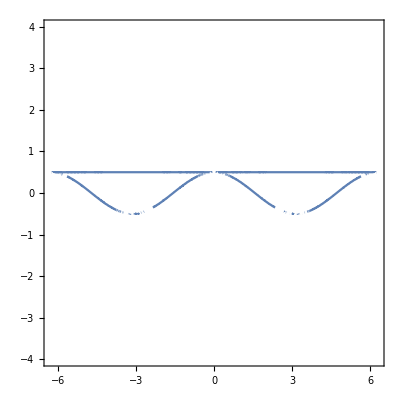

```mathematica
With[{t1=1.0,t2=0.5},ContourPlot[(t2^4-2 t2^2 ϵ^2+ϵ^4-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k])==0,{k,-2π,2π},{ϵ,-4,4},PlotPoints-> 100]]
```

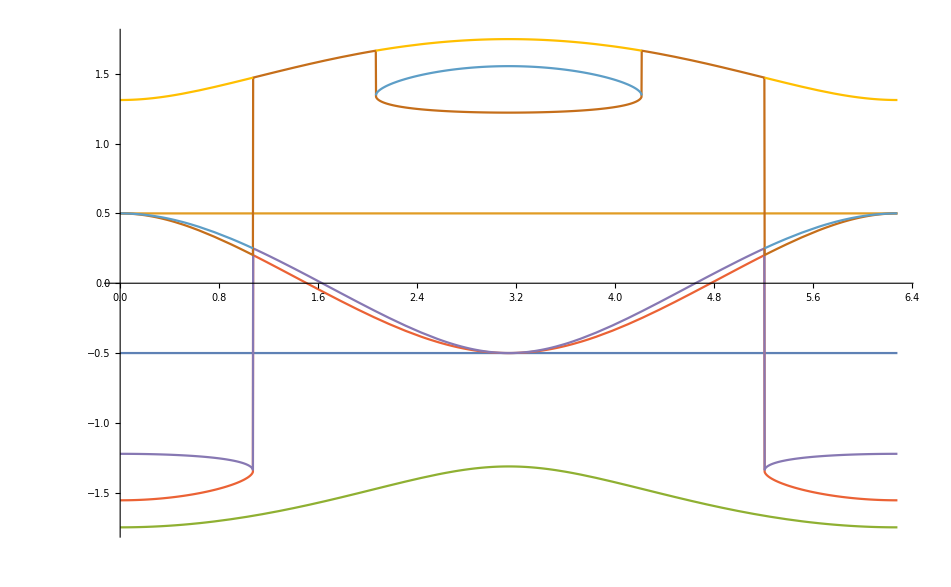

```mathematica
With[{t1=1.0,t2=0.5},Plot[{-t2,t2,Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,1],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,2],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,3],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,4],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,5],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,6],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,7],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,8],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,9],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,10],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,11],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,12]},{k,0,2 π}]]
```

```mathematica
ϵ/.Solve[((t2^4-2 t2^2 ϵ^2+ϵ^4)(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k])-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))==0,ϵ]
```

{-t2,t2,Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,1],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,2],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,3],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,4],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,5],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,6],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,7],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,8],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,9],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,10],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,11],Root[-8 t1^4 t2^2+t2^6-8 t1^4 t2^8-8 t1^4 t2^2 Cos[2 k]-8 t1^4 t2^8 Cos[2 k]+(32 t1^4 t2 Cos[k]+8 t1^2 t2^3 Cos[k]+32 t1^4 t2^7 Cos[k]+16 t1^2 t2^9 Cos[k]) #1+(-16 t1^4-8 t1^2 t2^2-3 t2^4+8 t1^4 t2^6-16 t1^2 t2^8-4 t2^10+24 t1^4 t2^6 Cos[2 k]) #1^2+(-8 t1^2 t2 Cos[k]-96 t1^4 t2^5 Cos[k]-64 t1^2 t2^7 Cos[k]) #1^3+(8 t1^2+3 t2^2+24 t1^4 t2^4+64 t1^2 t2^6+20 t2^8-24 t1^4 t2^4 Cos[2 k]) #1^4+(96 t1^4 t2^3 Cos[k]+96 t1^2 t2^5 Cos[k]) #1^5+(-1-40 t1^4 t2^2-96 t1^2 t2^4-40 t2^6+8 t1^4 t2^2 Cos[2 k]) #1^6+(-32 t1^4 t2 Cos[k]-64 t1^2 t2^3 Cos[k]) #1^7+(16 t1^4+64 t1^2 t2^2+40 t2^4) #1^8+16 t1^2 t2 Cos[k] #1^9+(-16 t1^2-20 t2^2) #1^10+4 #1^12&,12]}

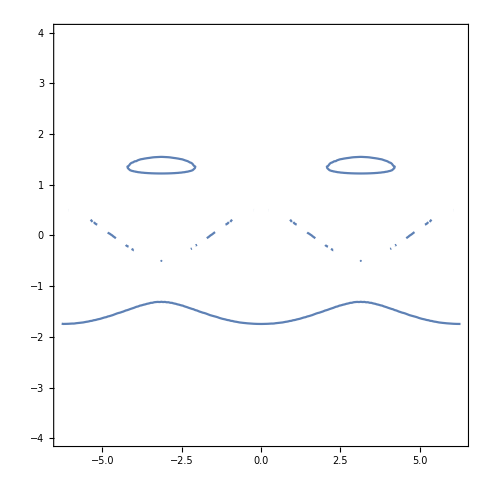

```mathematica
With[{t1=1.0,t2=0.5},ContourPlot[((t2^4-2 t2^2 ϵ^2+ϵ^4)(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k])-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))==0,{k,-2π,2π},{ϵ,-4,4}]]
```

```mathematica
With[{t1=1.0,t2=0.5},Plot3D[Abs[(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))],{k,-2π,2π},{ϵ,-4,4},PlotRange-> All]]
```

-Graphics3D-

```mathematica
With[{t1=1.0,t2=0.5},Plot[HeavisideTheta[1-1.01Abs[(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))]](t2^4-2 t2^2 ϵ^2+ϵ^4-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k])==0,{k,-2π,2π},{ϵ,-4,4}]]
```

```mathematica
Eigensystem[{{(ϵ (-4 t1^2 ϵ-t2^2 ϵ+ϵ^3+4 t1^2 t2 Cos[k]))/(2 t1^2 t2 (-ϵ+t2 Cos[k])),(ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k]))},{(-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k])),(t2 (t2^2-ϵ^2))/(2 t1^2 (-ϵ+t2 Cos[k]))}}]//Simplify
```

{{(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k])),(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))},{{-((t2^4+4 t1^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k]))),1},{(-t2^4-4 t1^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])),1}}}

```mathematica
With[{t1=.1,t2=1},Plot3D[Abs[(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))],{k,-2π,2π},{ϵ,-4,4},PlotRange-> All]]
```

-Graphics3D-

```mathematica
With[{t1=-0.5,t2=100},Plot3D[(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k])),{k,-2π,2π},{ϵ,-4,4}]]
```

-Graphics3D-